```mathematica
(*Some global parameters for plotting*)
myAxesSize=21;
myLabelSize=18;
myImageSize=1000;
SetDirectory[NotebookDirectory[]];
```

# P delta curve

### Reading solution and plotting

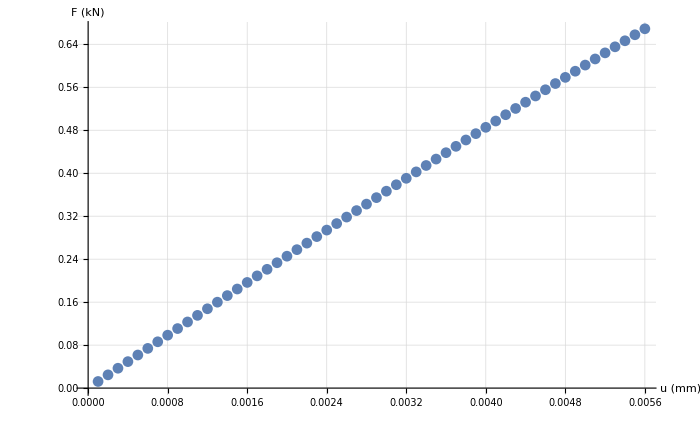

```mathematica
file=Import["build/pdelta_ex2.txt","Table"];
ListPlot[file,ImageSize->myImageSize 0.7,AxesLabel->{Style["u (mm)",myAxesSize,Black],Style["F (kN)",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*0.8,Bold,Black],GridLines->Automatic]
```